```mathematica
StepResponse[t_,τ_]:=√(1-ⅇ^(-t/τ))
Vbright = V[Transmission];
Vdark = V[Transmission/ContrastRatio];
Signal[t_]:=UnitStep[t]
PixelSpeed  :=0.0029;

Plot[Output[t],{t,0,0.05},AxesOrigin->{0,0},PlotRange->Full,Filling->True]
```

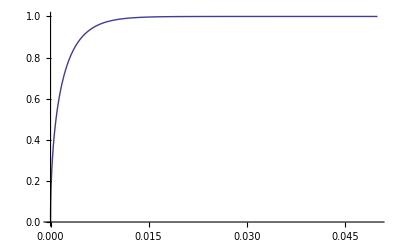

```mathematica
PixelSpeed  :=0.0029;
StepResponse[t_,τ_]:=√(1-ⅇ^(-t/τ))
ImpulseResponse[t_,τ_]=D[StepResponse[t,τ],t];

Signal[t_]:=SquareWave[{1,0},t]

Plot[StepResponse[t,PixelSpeed],{t,0,0.05}];
Output[t_]:=Convolve[ImpulseResponse[s,PixelSpeed],Signal[s],s,t]
(*Output2[t_]=NIntegrate[ImpulseResponse[t,PixelSpeed]*Signal[t-s],{s,-5,5}])*)
Plot[Output[t],{t,0,0.05},PlotRange->Full]
```